## Opakování

1.)

Vytvořte matici pomocí funkce Table (velikosti 7x7), pomocí matematického předpisu (i^(4*j))^(1/4).

	1) Pro zobrazení využijte funkci Grid. Ve výsledné matici budou nadpisy řádku i sloupců
	2) Nadpisy řádků a sloupců budou odděleny čárou od ostatního obsahu (čára oddělující nadpisy sloupců bude červeně, 	    čára oddělující názvy řádků bude modře. Obě čáry budou tečkovaně). Zbylé sloupce a řádky budou odděleny oranžovými čárami.
	3) Ohraničte oblast 3x3 v matici (od 3 sloupce do 6 sloupce, od 2 řádku do 5 řádku - pozor na přidané sloupce a řádky). 	    Vybranou oblast vybarvěte.

2.)

Vyzualizujte pomocí funkce Plot matematické funkce Sin x a Cos x v jednom grafu (0,2π).

	1) Vyplňte plochu mezi jednotlivými grafy.
	2) Popište osy grafu a přidejte název grafu a posuňte počátek souřadné soustavy o π (Osa x bude modrá, osa y bude 	    červená).
	3) Funkce Sin se bude vykreslovat tečkovaně a funkce Cos se bude vykreslovat čárkovaně

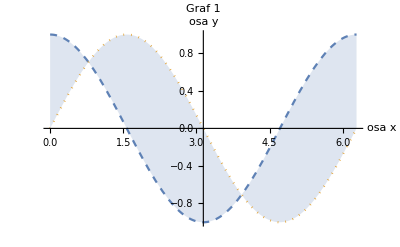

## Obsah hodiny

Plot

Pro vykreslení grafů funkcí v rovině využívá Mathematica funkce Plot[]. 

V argumentu funkce Plot[] musí být zadána nejdříve v prvním parametru vykreslovaná funkce a ve druhém parametru ve složených závorkách proměnná pro kterou je funkce vykreslována a meze této nezávislé proměnné, dále následuje výčet možného nastavení grafu (barvy, styl atd...nemusí být použito a graf je pak kreslen v základním nastavení).

viz Help k funkci Plot[].

Pozn.: Mnoho vlastností funkce Plot[], které jsou tady představeny jsou “univerzální” a vyskytují se i u jiných podobných funkcí (ListPlot[], Plot3D[], ListLinePlot[], ...)

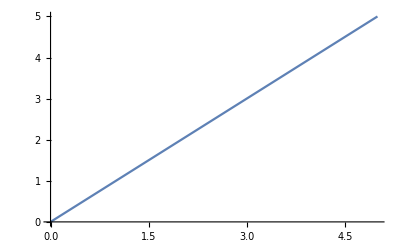

```mathematica
Plot[x,{x,0,5}]
```

Pozn.: Existují i verze Plot[] s logaritmickými osami:
	LogPlot[]		- Logaritmická osa y
	LogLogPlot[]		- Logaritmická osa x & y
	LogLinearPlot[]	- Logaritmická osa x

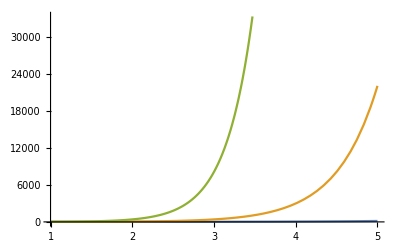

```mathematica
Plot[{ⅇ^x,ⅇ^(2x),ⅇ^(3x)},{x,1,5}]
```

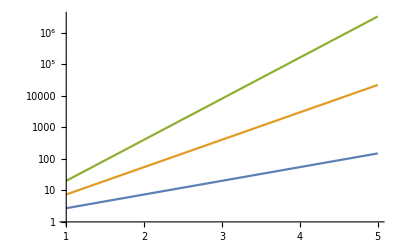

```mathematica
LogPlot[{ⅇ^x,ⅇ^(2x),ⅇ^(3x)},{x,1,5}]
```

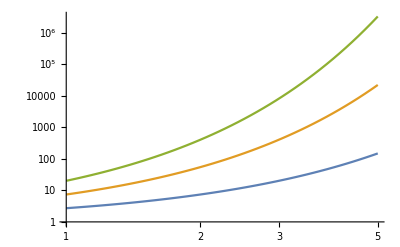

```mathematica
LogLogPlot[{ⅇ^x,ⅇ^(2x),ⅇ^(3x)},{x,1,5}]
```

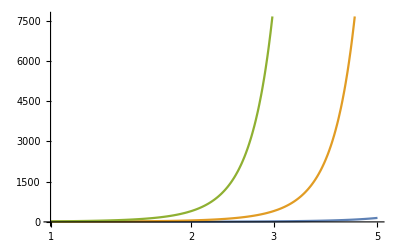

```mathematica
LogLinearPlot[{ⅇ^x,ⅇ^(2x),ⅇ^(3x)},{x,1,5}]
```

Následuje výčet pravděpodobně nejpoužívanějších vlastností funkce Plot[] s příkladem jejich použití.

#### Zobrazení více funkcí

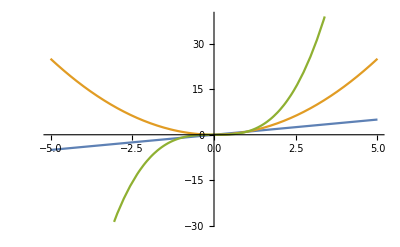

```mathematica
Plot[{x,x^2,x^3},{x,-5,5}]
```

#### PlotStyle

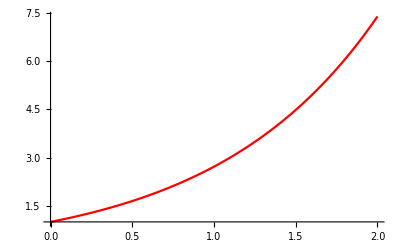

```mathematica
Plot[ⅇ^x,{x,0,2},
PlotStyle->Red
]
```

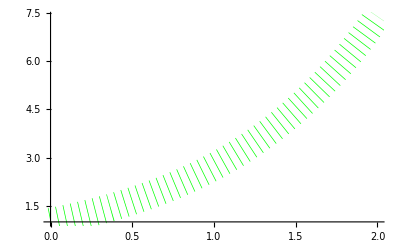

```mathematica
Plot[ⅇ^x,{x,0,2},
(* Funkce Directive[] sloužípro přiřazení více vlastností jednomu prvku *)
PlotStyle->Directive[Green,Dotted,Thickness@0.05]
]
```

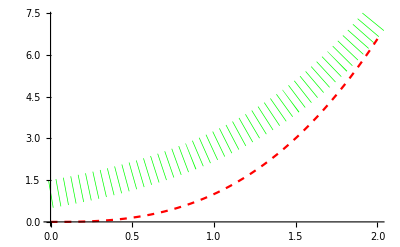

```mathematica
Plot[{ⅇ^x,x^ⅇ},{x,0,2},
PlotStyle->{
Directive[Green,Dotted,Thickness@0.05],
Directive[Red,Dashed]
}
]
```

#### PlotLegends

Zobrazení legendy grafu, pokud graf zobrazuje více jak jednu funkci.
Přebírá použité styly křivek.

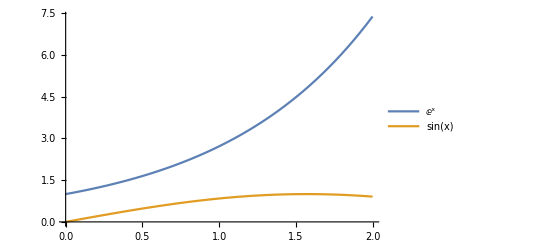

```mathematica
Plot[{ⅇ^x,Sin@x},{x,0,2},
PlotLegends->"Expressions"
]
```

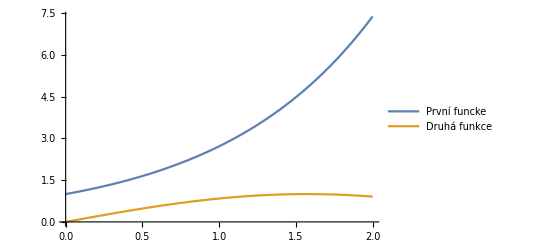

```mathematica
Plot[{ⅇ^x,Sin@x},{x,0,2},
PlotLegends->{"První funcke","Druhá funkce"}
]
```

#### Axes

Nastavení pro zobrazení os grafu

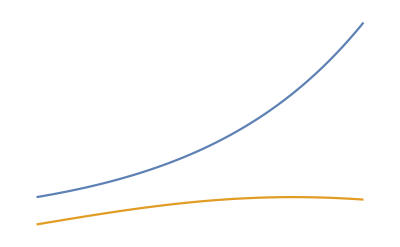

```mathematica
Plot[{ⅇ^x,Sin@x},{x,0,2},
Axes->False
]
```

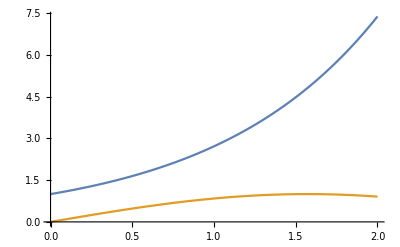

```mathematica
Plot[{ⅇ^x,Sin@x},{x,0,2},
Axes->{True,False}
]
```

#### AxesLabel

Pojmenování os grafu

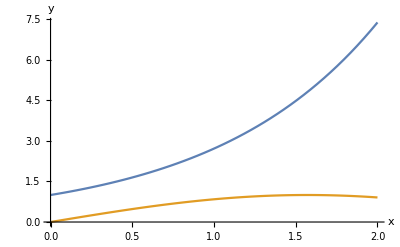

```mathematica
Plot[{ⅇ^x,Sin@x},{x,0,2},
AxesLabel->{"x","y"}
]
```

```mathematica
Plot[{ⅇ^x,Sin@x},{x,0,2},
(* funkce Style[] slouží k nastavení stylu fontu (textu) *)
AxesLabel->{Style["x",20,Italic,Brown],"y"}
]
```

-Graphics-

#### AxesOrigin

Nastavuje střed pro osy grafu

```mathematica
Plot[{ⅇ^x,Sin@x},{x,0,2},
AxesOrigin->{0,0}
]
```

-Graphics-

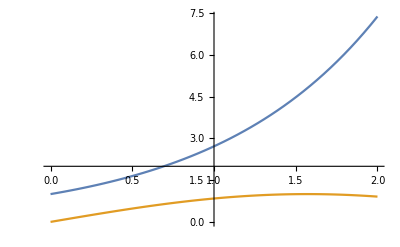

```mathematica
Plot[{ⅇ^x,Sin@x},{x,0,2},
AxesOrigin->{1,2}(*x,y*)
]
```

#### AxesStyle

Podobně jako PlotStyle[] nastavuje styl pro zobrazení os

```mathematica
Plot[{ⅇ^x,Sin@x},{x,0,2},
AxesStyle->DotDashed
]
```

-Graphics-

```mathematica
Plot[{ⅇ^x,Sin@x},{x,0,2},
AxesStyle->{
Red,
Directive[Orange, 20,Thickness@0.007]
}
]
```

-Graphics-

#### Filling

Nastavení pro výplň oblastí grafu

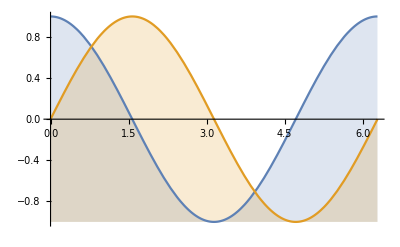

```mathematica
Plot[{Cos@x,Sin@x},{x,0,2π},
Filling->Bottom(* od funkce směrem "dolů" *)
]
```

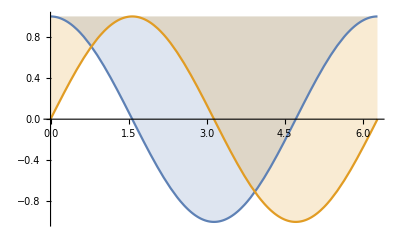

```mathematica
Plot[{Cos@x,Sin@x},{x,0,2π},
Filling->Top(* od funkce směrem "nahoru" *)
]
```

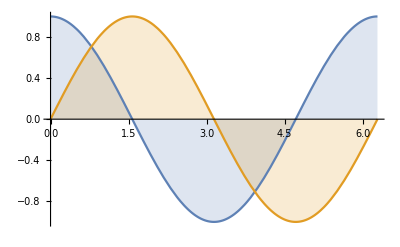

```mathematica
Plot[{Cos@x,Sin@x},{x,0,2π},
Filling->Axis(* od funkce směrem k ose x *)
]
```

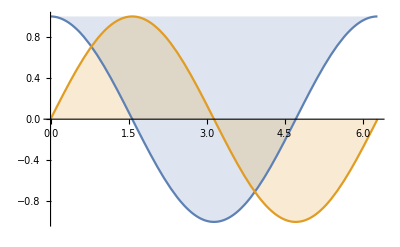

```mathematica
Plot[{Cos@x,Sin@x},{x,0,2π},
(* funkce 1.(Cos) má vlastnost Filling->Top a 2. funkce (Sin) Filling->Axis  *)
Filling->{1->Top,2->Axis}
]
```

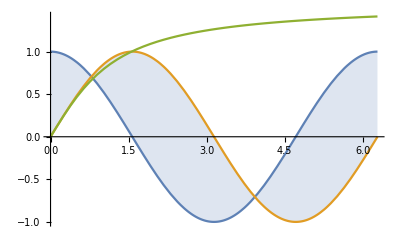

```mathematica
Plot[{Cos@x,Sin@x,ArcTan@x},{x,0,2π},
(* funkce 1.(Cos) vyplňuje oblast směrem ke 2. funkci (Sin)  *)
Filling->{1->{2}}
]
```

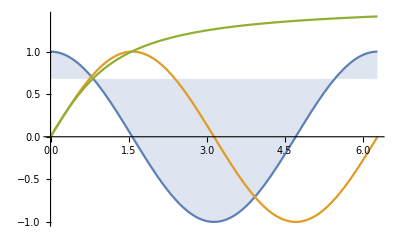

```mathematica
Plot[{Cos@x,Sin@x,ArcTan@x},{x,0,2π},
(* funkce 1.(Cos) vyplňuje oblast směrem k ⅇ/4  *)
Filling->{1->ⅇ/4}
]
```

#### FillingStyle

Slouží k nastavení stylu vyplňování

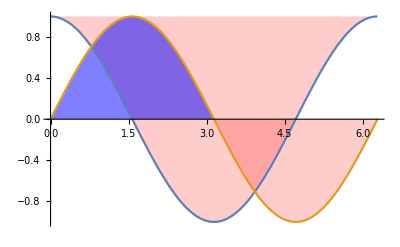

```mathematica
Plot[{Cos@x,Sin@x},{x,0,2π},
Filling->{1->Top,2->Axis},
FillingStyle->{
Red,
Directive[Blue,Opacity@0.5]
}
(* Opacity[] == průhlednost v rozsahu <0,1> *)
]
```

#### PlotLabel

Funkce pro nastavení názvu grafu

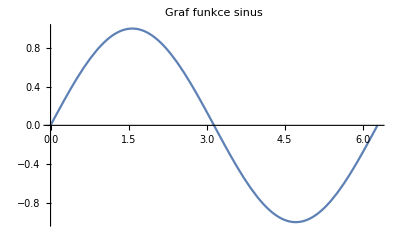

```mathematica
Plot[Sin@x,{x,0,2π},
PlotLabel->"Graf funkce sinus"
]
```

```mathematica
Plot[Sin@x,{x,0,2π},
PlotLabel->Style["Graf funkce sinus",20,Red,Bold,Underlined]
]
```

-Graphics-

#### PlotRange

Nastavuje rozsah zobrazení grafu

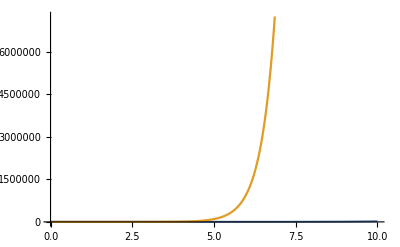

```mathematica
Plot[{ⅇ^x,10^x},{x,0,10},
PlotRange->Automatic
]
```

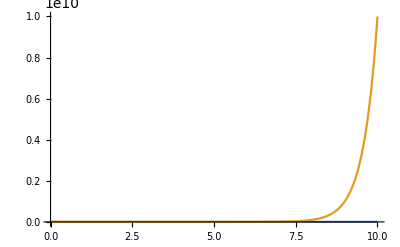

```mathematica
Plot[{ⅇ^x,10^x},{x,0,10},
PlotRange->Full
]
```

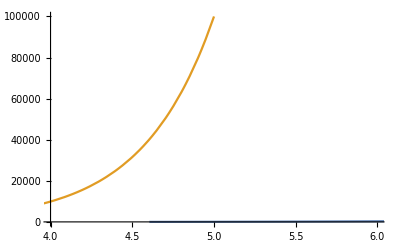

```mathematica
Plot[{ⅇ^x,10^x},{x,0,10},
(* zvlášť nastavuje rozsahy pro x a y *)
PlotRange->{
{4,6},
{100,100000}
}
]
```

#### GridLines

Zobrazení mřížky v grafu

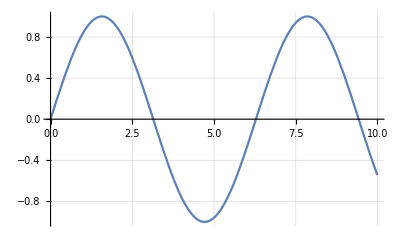

```mathematica
Plot[Sin@x,{x,0,10},
GridLines->Automatic
]
```

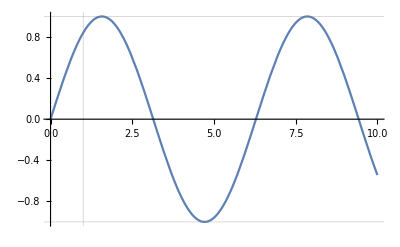

```mathematica
Plot[Sin@x,{x,0,10},
GridLines->{{-1,0,1}, {-1,0,1}}
]
```

#### GridLinesStyle

Nastavuje vzhled mřížky v grafu

```mathematica
Plot[Sin@x,{x,0,10},
GridLines->Automatic,
GridLinesStyle->Directive[Red, Dashed]
]
```

-Graphics-

#### Ticks

Nastavení zobrazovaných hodnot na osách grafu



```mathematica
Plot[Sin@x,{x,0,10},
Ticks->None
]
```

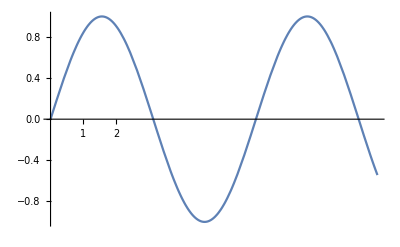

```mathematica
Plot[Sin@x,{x,0,10},
Ticks->{{1, 2}, Automatic}
]
```

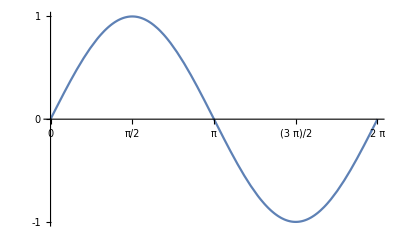

```mathematica
Plot[Sin@x,{x,0,2π},
Ticks->{{0,π/2,π,(3π)/2,2π}, {-1,0,1}}
]
```

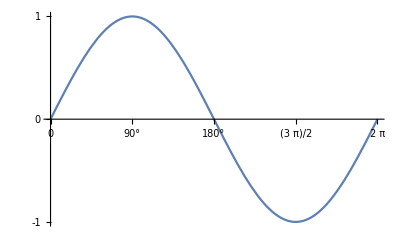

```mathematica
Plot[Sin@x,{x,0,2π},
(* hodnoty na osách můžeme i pojmenovat *)
Ticks->{
{0,{π/2,"90°"},{π,"180°"},(3π)/2,2π},
 {-1,0,1}
}
]
```

#### TicksStyle

Nastavení stylu hodnot na osách

```mathematica
Plot[Sin@x,{x,0,10},
TicksStyle->Red
]
```

-Graphics-

```mathematica
Plot[Sin@x,{x,0,10},
TicksStyle->{Red,Directive["Label", 14,Green]}
]
```

-Graphics-

ListPlot

ListPlot[] se hodí pokud chceme zobrazit v grafu data, které máme dané tabulkou (výčtem).
Co se vlastností týče, je mezi touto funkcí a Plot[] funkcí hodně podobností. Nicméně ListPlot[] obsahuje několik vlastností navíc, které si představíme.

Nejdříve potřebujeme data pro naši funkci ListPlot[]. jedná se o obyčejný List (vektor) hodnot.

```mathematica
data={1,2,3,4,5};
```

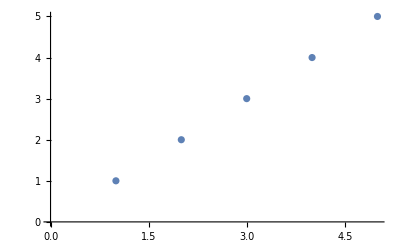

```mathematica
ListPlot[data]
```

Pokud jen zobrazíme jednorozměrný vektor tak funkce ListPlot[] automaticky každé hodnotě přiřadí číslo na ose x.

Funkce umí zobrazit i více vzorkl dat, podobně jako Plot[].

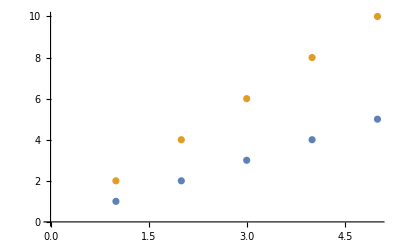

```mathematica
data1={2,4,6,8,10};
ListPlot[{data,data1}]
```

Pokud chceme, tak můžeme nastavit pro každý bod i hodnotu x.
Data pak budou ve  tvaru {{x_1,y_1},{x_2,y_2},...,{x_n,y_n}}

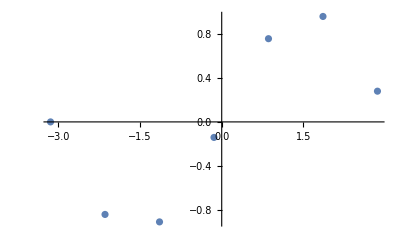

```mathematica
(*          {x,   y   }*)
data=Table[{x,Sin[x]},{x,-π,π}];
ListPlot[data]
```

Nezapomínjme, že v případě generování dat pomocí Table[] můžeme nastavit i velikost kroku, čili počet dat.

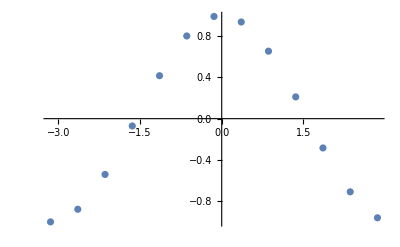

```mathematica
data1=Table[{x,Cos[x]},{x,-π,π,0.5}];
ListPlot[data1]
```

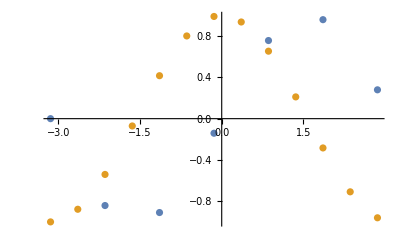

```mathematica
ListPlot[{data,data1}]
```

### Joined

Vlastnost funkce ListPlot[] pro “spojení” jednotlivých dat.

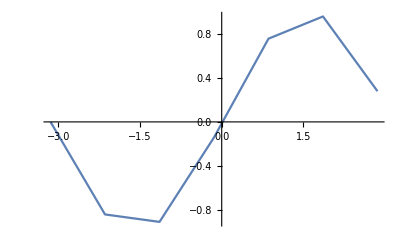

```mathematica
ListPlot[data,
Joined->True
]
```

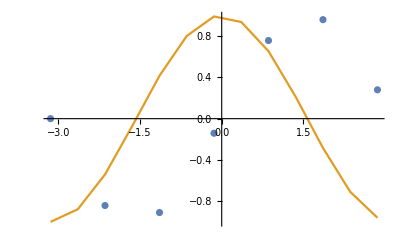

```mathematica
ListPlot[{data,data1},
(* spojení pouze druhého datasetu *)
Joined->{False,True}
]
```

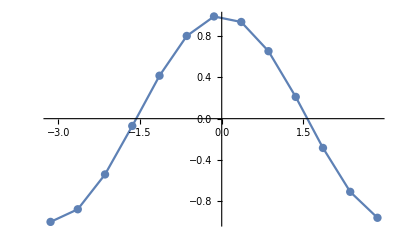

```mathematica
ListPlot[data1,
Joined->True,
(* zobrazení i samotných hodnot *)
Mesh->All
]
```

### PlotMarkers

Vlastnost pro změnu vzhledu bodů hodnot v grafu

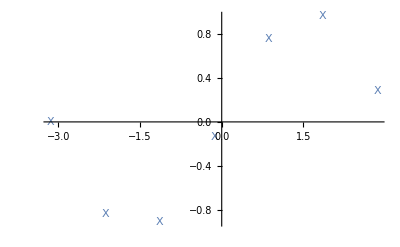

```mathematica
ListPlot[data,
PlotMarkers->"X"
]
```

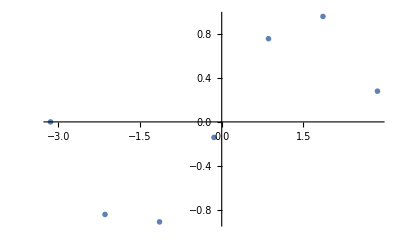

```mathematica
ListPlot[data,
(* můžeme zadat jak vzhled bodů tak i jejich velikost *)
PlotMarkers->{"♥",30}
]
```

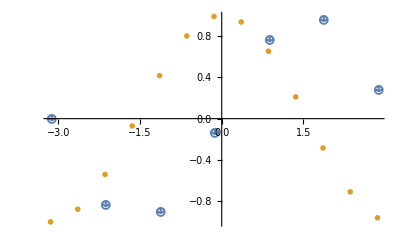

```mathematica
ListPlot[{data,data1},
PlotMarkers->{
"☻",
{"☺",20}
}
]
```

Pozn.: Jako bod může teoreticky sloužit jakýkoli objekt v Mathematice.

```mathematica
ListPlot[data,
PlotMarkers->-Graphics-
]
```

-Graphics-

Show

Funkce Show[] slouží ke spojení dvou a více grafických prvků (typicky grafů) do jednoho celku.
Tato kombinace funguje jen u “podobných” objektů. Např. Plot[] & ListPlot[].
Výsledný objekt přebírá nastavení vlastnosti (pokud oba objekty tuto ovlastnost mají) z prvního objektu v seznamu.

Pro ukázku si vytvořme dva grafy stejné funkce, jednou pomocí ListPlot[] a podruhé pomocí Plot[] a každému grafu nastavíme různé vlastnosti.

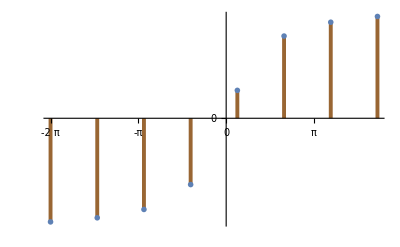

```mathematica
data=Table[{x,ArcTan@x},{x,-2π,2π,0.1+0.5π}];
g1=ListPlot[data,
PlotMarkers->{Graphics[{Red,Annulus[]}],0.1},
Filling->Axis,
FillingStyle->Directive[Brown,Thickness@0.007],
Axes->{True,False},
Ticks->{Table[i,{i,-2π,2π,π}]},
TicksStyle->Directive[Black, 20]
]
```

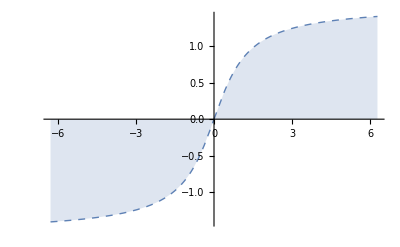

```mathematica
g2=Plot[ArcTan@x,{x,-2π,2π},
PlotStyle->Directive[
Dashed,Thick
],
Filling->Axis
]
```

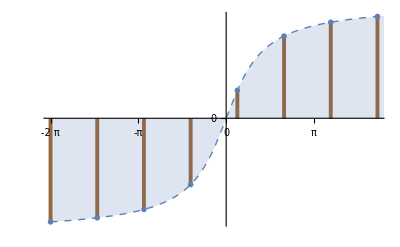

```mathematica
(* výsledná kombinace dvou grafů *)
Show@{g1,g2}
```

Plot3D

Lehký úvod

Funkce Plot[] a její varianty do teď probrané vždy pracovaly v tzv. 2D prostoru, kde máme 2 osy souřadnic (x, y).
Pro 3D variantu existují funkce jako Plot3D[], ListPlot3D[] a mnoho dalších.

Z celkem jasného důvodu (2D vs 3D) je mnoho vlastností jiných nebo mají jiné nastavení.

```mathematica
Plot3D[x+y,{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y],{x,0,2π},{y,0,2π}]
```

-Graphics3D-

## Samostatné úkoly

1.)

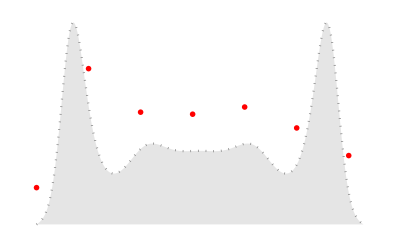
Vytvořte následující graf:
y_(x) = Sin[x]^Cos[8x]
x ϵ <0, π>
-Graphics-

Nápověda:
		Jde o dva spojené grafy (Plot[] a ListPlot[])
		
	Vlastnosti, které je potřeba upravit:
		Axes
		Ticks
		AxesStyle
		PlotStyle
		PlotMarkers
		Filling

2.)

Vytvořte 3D graf podle funkce Sin(2x)-Cos(2x-y)+Sin(x^3) v intervalu x ϵ (0,3) a y ϵ (0,3). 
	a) Vytvořte popisky os a název grafu. Navíc nastavte jemnost vykreslované sítě na 50, pro vyhlazení grafu.
	b) Nastavte úhel pohledu na (1,2,1).
	c) Vytvořte síť (mřížku) jenom pod vykreslovaným grafem.
	d) Výsledný graf vybarvěte barvami v závislosti na ose z.